## co prop 1.7W 3.4 vs 3.3 mW/mK 750 vs 970nm want the ULat to be much bigger than atom temp... ie 10uK.

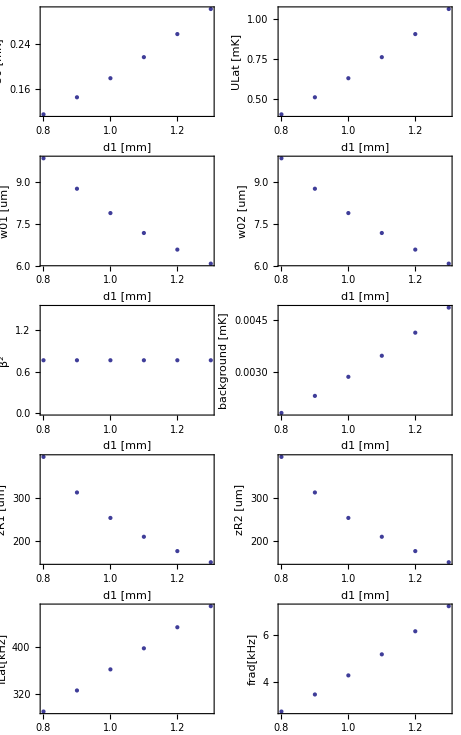

```mathematica
(*1=forw, 2=retro*)
Clear["Global`*"];
data=Reap[
Do[
nm=10^-9;
um=10^-6;
mW=10^-3;
mK=10^-3;
cm=10^-2;
kHz=10^3;
amu=1.66054 10^-27;

kB=1.38064852 10^-23;
m=132.90545 amu;


λ=775nm;
f2 = 50mm;
f1=16mm;

R =18mm/2;(*aperture of retro lens*)
R=R;(*just to account for clipping*)

w2=w1 f2/f1; (*waist of forward beam AT retro lens = waist of retro input beam*)
NA1=w1/f1;

NA2=Min[w2/f2,R/f2];
w01=λ/(π NA1); (*waist at focus of forw beam*)
w02=λ/(π NA2);
zR1=w01/NA1; 
zR2=w01/NA2;

Pin = 71.5mW;
U0=0.6mK  (Pin/(3 mW))3.3/2.7(800nm/w01)^2; (*bare lattice beam (no retro)*)
(*Pretrofrac=1-ⅇ^(-(2 R^2)/w2^2);(*fraction of power of a beam of waist w transmitted thru an aperture of radius R*)
β=√Pretrofrac.5 ; (*ratio of retro E field to forw E field x some attenuation factor (experimental)*)
*)
β=√(62.8/82.3); (*actual measured power right before retro mirror/ right before objective*)
ULat=4U0 NA2/NA1 β;

d=2U0 NA2/NA1 β Cos[(4 π z)/λ]; (*functional form of lattice potential*)
a=Normal[Series[d,{z,0,2}]]; (*harmonic approx*)

(*bare forward lattice beam only*)
frad=√(Abs[kB U0]/(m (π  w01)^2));
fax=(λ frad)/(√2 π w01);

fLat=fLat0/.Solve[-1/2 m(2π fLat0)^2==kB Coefficient[a,z^2],fLat0][[2]]; (*lattice freqs*)

Sow[{2w1/mm,U0/mK,ULat/mK,β^2,w01/um,w02/um,U0(1-NA2/NA1 β)^2/mK,zR1/um,zR2/um,fLat/kHz,frad/kHz}]
,{w1,.8mm/2,1.3mm/2,.05mm}]
][[2,1]];
GraphicsGrid[{
{
ListPlot[data[[All,{1,2}]],Axes->False,Frame->True,FrameLabel->{"d1 [mm]","U0 [mK]","f2="<>ToString[f2/mm]<>"mm"}],
ListPlot[data[[All,{1,3}]],Axes->False,Frame->True,FrameLabel->{"d1 [mm]","ULat [mK]"}]
},
{
ListPlot[data[[All,{1,5}]],Axes->False,Frame->True,FrameLabel->{"d1 [mm]","w01 [um]"}],
ListPlot[data[[All,{1,6}]],Axes->False,Frame->True,FrameLabel->{"d1 [mm]","w02 [um]"}]

},
{
ListPlot[data[[All,{1,4}]],Axes->False,Frame->True,FrameLabel->{"d1 [mm]","β^2"}],
ListPlot[data[[All,{1,7}]],Axes->False,Frame->True,FrameLabel->{"d1 [mm]","background [mK]"}]
},
{
ListPlot[data[[All,{1,8}]],Axes->False,Frame->True,FrameLabel->{"d1 [mm]","zR1 [um]"}],
ListPlot[data[[All,{1,9}]],Axes->False,Frame->True,FrameLabel->{"d1 [mm]","zR2 [um]"}]
},
{
ListPlot[data[[All,{1,10}]],Axes->False,Frame->True,FrameLabel->{"d1 [mm]","fLat[kHz]"}],
ListPlot[data[[All,{1,11}]],Axes->False,Frame->True,FrameLabel->{"d1 [mm]","frad[kHz]"}]
}

}
]
```

## check scattering rate

```mathematica
MHz=10^6;
s=Pin/(π w01^2)/(2.7 mW/cm^2);
Γ =32 MHz;
Δ = 2π 3. 10^8(852-780)/852^2 1/nm;
Γ/2 s/(1+s+((2 Δ)/Γ)^2)
```

0.374646